### Data Extraction:

```mathematica
data=Import["C:\\Users\\thema\\Downloads\\Outreach Analysis - Sheet1.csv"];
pretest=data[[All,1]];
posttest=data[[All,2]];
```

### Descriptive Stats:

```mathematica
meanpre=  N[Mean[pretest]]
meanpost=N[Mean[posttest]]
medianpre=N[Median[pretest]]
medianpost=N[Median[posttest]]
modepre=Commonest[pretest]
modepost=Commonest[posttest]
standpre=N[StandardDeviation[pretest]]
standpost=N[StandardDeviation[posttest]]
varpre=N[Variance[pretest]]
varpost=N[Variance[posttest]]
```

15.5777

25.5972

15.

25.

{15}

{35}

9.65644

10.2974

93.2468

106.036

### ECDF Plot:

ECDF (Empirical Cumulative Distribution Function) plots are used to visualize the distribution of data and compare different datasets. They display the data points in your sample from lowest to highest against their percentiles. Unlike histograms, ECDFs show a single variable distribution in a more efficient way as each observation is visualized directly.

The first ECDF plot (pre-test) shows a steeper curve, indicating a more concentrated distribution of scores.
The second ECDF plot (post-test) has a gentler slope, suggesting that scores are more spread out.

This suggests that there’s an improvement in performance diversity from pre-test to post-test.

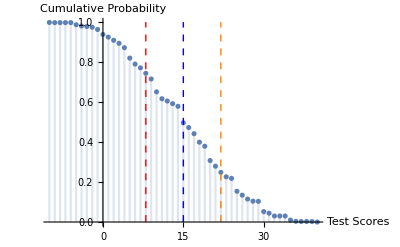

```mathematica
ecdf=EmpiricalDistribution[data[[All,1]]];

(*Find quartiles*)
quartiles=Quartiles[data[[All,1]]];
Show[DiscretePlot[1-CDF[ecdf,x],{x,Min[data[[All,1]]],Max[data[[All,1]]]},PlotRange->All,AxesLabel->{"Test Scores","Cumulative Probability"}],Graphics[{Red,Dashed,Line[{{quartiles[[1]],0},{quartiles[[1]],1}}]}],Graphics[{Blue,Dashed,Line[{{quartiles[[2]],0},{quartiles[[2]],1}}]}],Graphics[{Orange,Dashed,Line[{{quartiles[[3]],0},{quartiles[[3]],1}}]}]]
```

```mathematica
(*Compute ECDF*)
ecdf=EmpiricalDistribution[data[[All,2]]];

(*Find quartiles*)
quartiles=Quartiles[data[[All,2]]];

(*Plot ECDF with quartiles*)
Show[DiscretePlot[1-CDF[ecdf,x],{x,Min[data[[All,2]]],Max[data[[All,2]]]},PlotRange->All,AxesLabel->{"Test Scores","Cumulative Probability"}],Graphics[{Red,Dashed,Line[{{quartiles[[1]],0},{quartiles[[1]],1}}]}],Graphics[{Blue,Dashed,Line[{{quartiles[[2]],0},{quartiles[[2]],1}}]}],Graphics[{Orange,Dashed,Line[{{quartiles[[3]],0},{quartiles[[3]],1}}]}]]
```

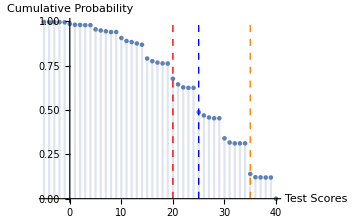

### T-Test

The T-Test is a Two-Sample Assuming Unequal Variances test (Welch’s t-test), which is used when the variances of the two groups being compared are assumed to be different. Here’s how to interpret the results:

1) t Stat: The t Stat value is negative, indicating that the mean of the post-test is significantly higher than the pre-test.
2) P(T<=t) one-tail: The p-value for a one-tailed t-test is less than 0.05, indicating that we can reject the null hypothesis that there’s no difference in means at a 95% confidence level. This means there is a statistically significant difference in the means of the pre-test and post-test groups.
3) t Critical one-tail: This is the critical value of the test. If the absolute value of the t Stat is greater than the t Critical one-tail, we reject the null hypothesis. In this case, it appears that the t Stat is less than the t Critical one-tail, suggesting that we fail to reject the null hypothesis.

```mathematica
TTest[{pretest, posttest}, Automatic,{"DegreesOfFreedom","PValueTable","TestDataTable","TestStatisticTable"}]
```

{2252.72, | P-Value
T | 1.54963×10^-112, | Statistic | P-Value
T | -23.8799 | 1.54963×10^-112, | Statistic
T | -23.8799}

### Correlation:

Correlation is typically used to measure covariation, i.e. whether one variable tends to vary similarly to another.
Correlation coefficients whose magnitude are between 0.5 and 0.7 indicate variables which can be considered moderately correlated.
(here, 0.54995004915)

```mathematica
correlationMatrix=Correlation[data]
```

{{1,1/1131((302041821757 √(2/56274481013027))/283+(4324528169 √(37/3041863838542))/566+(651816035 √(74/1520931919271))/283+2270205228941/(566 √112548962026054))},{1/1131((302041821757 √(2/56274481013027))/283+(4324528169 √(37/3041863838542))/566+(651816035 √(74/1520931919271))/283+2270205228941/(566 √112548962026054)),1}}

```mathematica
correlation=N[Correlation[data[[All,1]],data[[All,2]]]]
```

0.54995

```mathematica
xData=data[[All,1]];
yData=data[[All,2]];
fit=Fit[Transpose[{xData,yData}],{1,x},x]
```

16.4616+0.586452 x

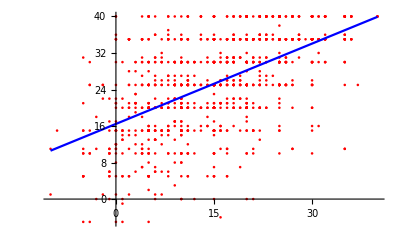

```mathematica
Show[ListPlot[data,PlotStyle->Red],Plot[fit,{x,Min[xData],Max[xData]},PlotStyle->Blue]]
```

### NonLinearModelFit (An Attempt to perform Non-Linear Regression)

NonlinearModelFit is a function in Mathematica that constructs a nonlinear model for data. It’s a generalization of the built-in Fit function to handle nonlinear cases.
NonlinearModelFit[data, form, params, vars] constructs a nonlinear model with formula form that fits the y_i for each x_i using the free parameters βi.

```mathematica
nlm=NonlinearModelFit[data,a*x^2+b*x+c,{a,b,c},x];
nlm[x]
```

16.0436+0.672736 x-0.00275778 x^2

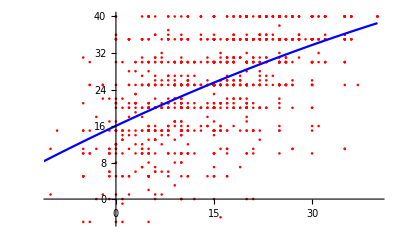

```mathematica
Show[ListPlot[data,PlotStyle->Red],Plot[nlm[x],{x,-40,40},PlotStyle->Blue]]
```

```mathematica
newPrediction=Predict[nlm,37]
```

37.1594

```mathematica
newPrediction=Predict[nlm,10]
```

22.4952

#### Verifying Accuracy of NLM Model (Residual Analysis & R-squared and Adjusted R-squared):

This code will perform non-linear regression on a simulated dataset, plot the model, and provide diagnostic plots for residuals. 

The accuracy of a model is not determined solely by the model itself, but also by how well it fits the data. Therefore, always check the residuals and Cook’s distances to ensure your model is a good fit for your data.

A well-fitted model will have residuals that are randomly scattered around zero, indicating that the model adequately captures the relationship between the independent and dependent variables. {Check Residuals with Orange Colour in Residual_Analysis graph}

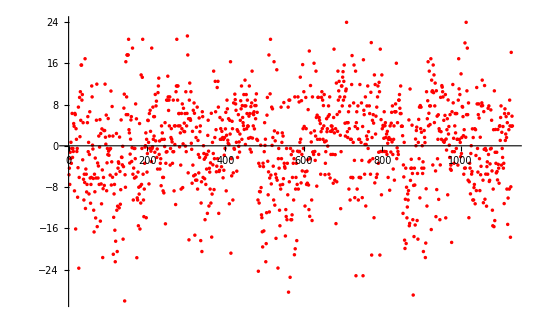

```mathematica
residuals=data[[All,2]]-nlm["PredictedResponse"];
ListPlot[residuals, PlotStyle->Red]
```

```mathematica
nlm["ANOVATable"]
```

| DF | SS | MS
Model | 3 | 778075. | 259358.
Error | 1129 | 83554.6 | 74.0077
Uncorrected Total | 1132 | 861630. | 
Corrected Total | 1131 | 119926. |

### Conceptual Analysis using Bar Graphs:

Note:  The Data has been collected from the forms and successfully divided the sets and gathered the question-wise in a spreadsheet. We’re only dealing with there averages in percent here.

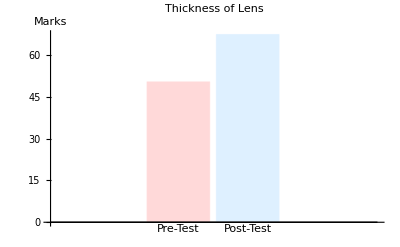

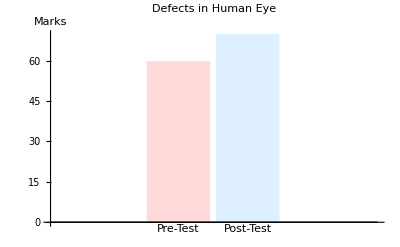

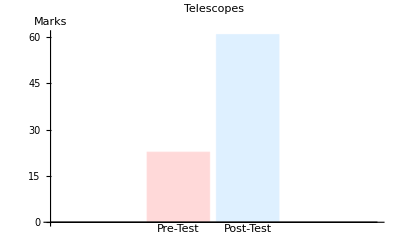

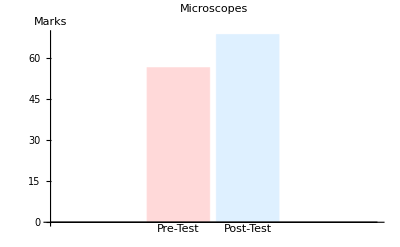

```mathematica
Q4and6={50.32443702, 67.31310288};
Q7= {59.62733566, 69.6564574};
Q8and9={22.68592867, 60.72049752};
Q10={56.46423906, 68.55781645};

A=BarChart[Q4and6,ChartLabels->{"Pre-Test","Post-Test"},ChartStyle->{LightRed, LightBlue},AxesLabel->{,"Marks"}, PlotLabel->"Thickness of Lens"]
B=BarChart[Q7,ChartLabels->{"Pre-Test","Post-Test"},ChartStyle->{LightRed, LightBlue},AxesLabel->{,"Marks"}, PlotLabel->"Defects in Human Eye"]
CA=BarChart[Q8and9,ChartLabels->{"Pre-Test","Post-Test"},ChartStyle->{LightRed, LightBlue},AxesLabel->{,"Marks"}, PlotLabel->"Telescopes"]
DA=BarChart[Q10,ChartLabels->{"Pre-Test","Post-Test"},ChartStyle->{LightRed, LightBlue},AxesLabel->{,"Marks"}, PlotLabel->"Microscopes"]
```

### Feedback Analysis

Note:  The Data has been collected from the forms and successfully divided the sets and gathered the question-wise in a spreadsheet. We’re only dealing with there means here.

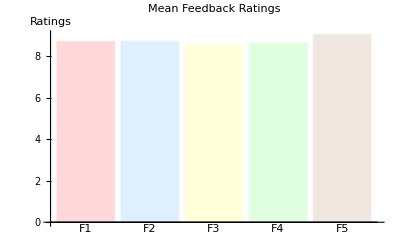

```mathematica
dataFeedback={8.696,8.709,8.537,8.618,9.028};
BarChart[dataFeedback,ChartLabels->{"F1","F2","F3","F4","F5"},ChartStyle->{LightRed, LightBlue,LightYellow,LightGreen,LightBrown},AxesLabel->{,"Ratings"},PlotLabel->"Mean Feedback Ratings"]
```